9.81

9.81 m

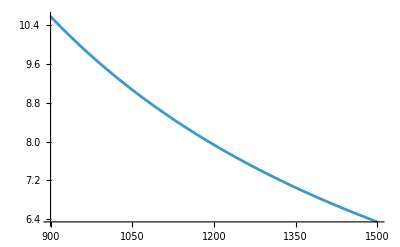

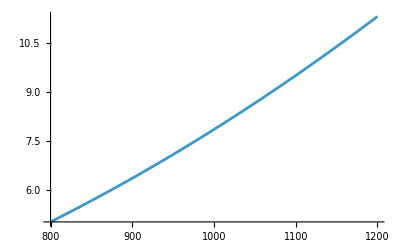

```mathematica
ClearAll["Global`*"]
g=9.81
Fg=m*g
c[v_]:=v*10/36
Fod[r_,v_]:=m*c[v]^2/r
stosunek[r_,v_]:=Fod[r,v]/Fg
(**)
Plot[stosunek[r,1100],{r,900,1500}]
Plot[stosunek[1000,v],{v,800,1200}]
```